In this notebook, a bilayer is considered. 
The exchange in the bottom half is larger than on the top half. 

We apply the SAME DMI strength on the top and bottom, to show that the shift in the frequencies are not equal.
All the raw data is on the bottom. Figure 8 of the article is produced at the end.

## The Eigenfrequencies -- Fe -- D = 3.9 mJ/m^2. TOP

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=20;
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=1750000; (*A/m*)
AA=1.88 10^-11;  (*J/m*)
DD =3.9 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

349.338

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,4 JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=2 DD/(a Ms);
HDMI[LL]=0
```

0

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

#### Dispersion plots

```mathematica
freqs2[LL,100 10 a,0,0.5]
```

{-20.9668,20.9668,-476.439,476.439,-2068.47,2068.47,-4844.35,4844.35,-6623.59,6623.59,-10767.4,10767.4,-15472.7,15472.7,-18491.3,18491.3,-23359.9,23359.9,-28566.6,28566.6,-32331.4,32331.4,-35309.2,35309.2,-38058.7,38058.7,-43351.7,43351.7,60179.,-60179.,82442.,-82442.,-105248.,105248.,125937.,-125937.,-142386.,142386.,-152955.,152955.}

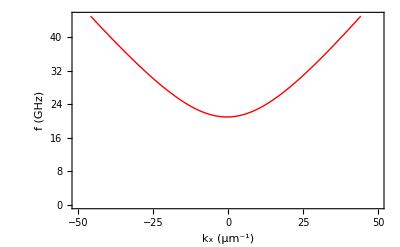

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-50 10^6,50 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->{0,45},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-50 10^6,50 10^6,1 10^6}]
```

{{-50,48.2429},{-49,47.4648},{-48,46.6894},{-47,45.9169},{-46,45.1474},{-45,44.3812},{-44,43.6184},{-43,42.8593},{-42,42.104},{-41,41.3528},{-40,40.606},{-39,39.8639},{-38,39.1267},{-37,38.3947},{-36,37.6684},{-35,36.9479},{-34,36.2338},{-33,35.5264},{-32,34.8262},{-31,34.1336},{-30,33.4491},{-29,32.7733},{-28,32.1068},{-27,31.4501},{-26,30.8039},{-25,30.169},{-24,29.5461},{-23,28.936},{-22,28.3395},{-21,27.7576},{-20,27.1912},{-19,26.6413},{-18,26.1091},{-17,25.5957},{-16,25.1022},{-15,24.6299},{-14,24.1801},{-13,23.7541},{-12,23.3533},{-11,22.979},{-10,22.6326},{-9,22.3154},{-8,22.0288},{-7,21.774},{-6,21.5522},{-5,21.3646},{-4,21.212},{-3,21.0954},{-2,21.0153},{-1,20.9724},{0,20.9668},{1,20.9987},{2,21.068},{3,21.1744},{4,21.3174},{5,21.4963},{6,21.7103},{7,21.9585},{8,22.2396},{9,22.5526},{10,22.8962},{11,23.269},{12,23.6698},{13,24.0971},{14,24.5495},{15,25.0258},{16,25.5245},{17,26.0445},{18,26.5845},{19,27.1433},{20,27.7197},{21,28.3127},{22,28.9213},{23,29.5444},{24,30.1813},{25,30.8309},{26,31.4926},{27,32.1655},{28,32.849},{29,33.5424},{30,34.2451},{31,34.9565},{32,35.6761},{33,36.4033},{34,37.1378},{35,37.879},{36,38.6266},{37,39.3802},{38,40.1394},{39,40.9038},{40,41.6733},{41,42.4475},{42,43.2261},{43,44.0088},{44,44.7955},{45,45.5859},{46,46.3798},{47,47.177},{48,47.9772},{49,48.7805},{50,49.5865}}

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]]+If[freqs2[LL,ky a,0,0.5][[1]]<0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-50 10^6,50 10^6,1 10^6}]
```

{{-50,-1.34355},{-49,-1.31566},{-48,-1.28784},{-47,-1.26007},{-46,-1.23236},{-45,-1.20471},{-44,-1.17712},{-43,-1.14958},{-42,-1.12209},{-41,-1.09466},{-40,-1.06727},{-39,-1.03994},{-38,-1.01266},{-37,-0.985424},{-36,-0.958235},{-35,-0.931092},{-34,-0.903993},{-33,-0.876937},{-32,-0.849922},{-31,-0.822948},{-30,-0.796014},{-29,-0.769117},{-28,-0.742257},{-27,-0.715432},{-26,-0.688642},{-25,-0.661885},{-24,-0.63516},{-23,-0.608465},{-22,-0.581799},{-21,-0.555162},{-20,-0.528551},{-19,-0.501965},{-18,-0.475404},{-17,-0.448866},{-16,-0.42235},{-15,-0.395854},{-14,-0.369377},{-13,-0.342918},{-12,-0.316476},{-11,-0.290049},{-10,-0.263636},{-9,-0.237236},{-8,-0.210847},{-7,-0.184469},{-6,-0.1581},{-5,-0.131738},{-4,-0.105383},{-3,-0.0790325},{-2,-0.0526862},{-1,-0.0263425},{0,2.13163×10^-14},{1,0.0263425},{2,0.0526862},{3,0.0790325},{4,0.105383},{5,0.131738},{6,0.1581},{7,0.184469},{8,0.210847},{9,0.237236},{10,0.263636},{11,0.290049},{12,0.316476},{13,0.342918},{14,0.369377},{15,0.395854},{16,0.42235},{17,0.448866},{18,0.475404},{19,0.501965},{20,0.528551},{21,0.555162},{22,0.581799},{23,0.608465},{24,0.63516},{25,0.661885},{26,0.688642},{27,0.715432},{28,0.742257},{29,0.769117},{30,0.796014},{31,0.822948},{32,0.849922},{33,0.876937},{34,0.903993},{35,0.931092},{36,0.958235},{37,0.985424},{38,1.01266},{39,1.03994},{40,1.06727},{41,1.09466},{42,1.12209},{43,1.14958},{44,1.17712},{45,1.20471},{46,1.23236},{47,1.26007},{48,1.28784},{49,1.31566},{50,1.34355}}

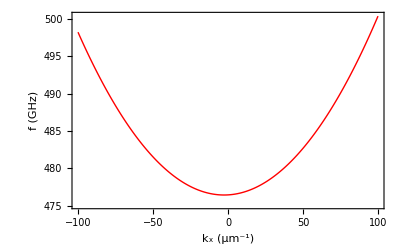

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[3]]>0,freqs2[LL,ky a,0,0.5][[3]],freqs2[LL,ky a,0,0.5][[4]]] },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->All,LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[3]]>0,freqs2[LL,ky a,0,0.5][[3]],freqs2[LL,ky a,0,0.5][[4]]] },{ky,-100 10^6,100 10^6,1 10^6}]
```

{{-100,498.252},{-99,497.799},{-98,497.352},{-97,496.91},{-96,496.473},{-95,496.04},{-94,495.613},{-93,495.19},{-92,494.772},{-91,494.359},{-90,493.95},{-89,493.547},{-88,493.148},{-87,492.755},{-86,492.366},{-85,491.982},{-84,491.602},{-83,491.228},{-82,490.858},{-81,490.493},{-80,490.133},{-79,489.778},{-78,489.427},{-77,489.082},{-76,488.741},{-75,488.404},{-74,488.073},{-73,487.746},{-72,487.424},{-71,487.107},{-70,486.794},{-69,486.486},{-68,486.183},{-67,485.885},{-66,485.591},{-65,485.303},{-64,485.018},{-63,484.739},{-62,484.464},{-61,484.194},{-60,483.929},{-59,483.668},{-58,483.412},{-57,483.16},{-56,482.914},{-55,482.672},{-54,482.434},{-53,482.201},{-52,481.973},{-51,481.75},{-50,481.531},{-49,481.317},{-48,481.107},{-47,480.903},{-46,480.702},{-45,480.507},{-44,480.316},{-43,480.129},{-42,479.948},{-41,479.77},{-40,479.598},{-39,479.43},{-38,479.266},{-37,479.108},{-36,478.954},{-35,478.804},{-34,478.659},{-33,478.519},{-32,478.383},{-31,478.251},{-30,478.125},{-29,478.003},{-28,477.885},{-27,477.772},{-26,477.664},{-25,477.56},{-24,477.46},{-23,477.366},{-22,477.276},{-21,477.19},{-20,477.109},{-19,477.032},{-18,476.96},{-17,476.893},{-16,476.83},{-15,476.771},{-14,476.718},{-13,476.668},{-12,476.623},{-11,476.583},{-10,476.548},{-9,476.516},{-8,476.49},{-7,476.467},{-6,476.45},{-5,476.437},{-4,476.428},{-3,476.424},{-2,476.425},{-1,476.43},{0,476.439},{1,476.453},{2,476.472},{3,476.495},{4,476.522},{5,476.554},{6,476.591},{7,476.632},{8,476.678},{9,476.728},{10,476.783},{11,476.842},{12,476.906},{13,476.974},{14,477.047},{15,477.124},{16,477.206},{17,477.292},{18,477.383},{19,477.478},{20,477.578},{21,477.682},{22,477.791},{23,477.905},{24,478.023},{25,478.145},{26,478.272},{27,478.404},{28,478.54},{29,478.68},{30,478.825},{31,478.975},{32,479.129},{33,479.288},{34,479.451},{35,479.619},{36,479.791},{37,479.968},{38,480.15},{39,480.336},{40,480.526},{41,480.721},{42,480.921},{43,481.125},{44,481.334},{45,481.547},{46,481.765},{47,481.987},{48,482.215},{49,482.446},{50,482.682},{51,482.923},{52,483.168},{53,483.418},{54,483.673},{55,483.932},{56,484.196},{57,484.464},{58,484.737},{59,485.014},{60,485.296},{61,485.583},{62,485.874},{63,486.17},{64,486.471},{65,486.776},{66,487.086},{67,487.4},{68,487.72},{69,488.043},{70,488.372},{71,488.705},{72,489.042},{73,489.385},{74,489.732},{75,490.083},{76,490.44},{77,490.801},{78,491.167},{79,491.537},{80,491.912},{81,492.292},{82,492.676},{83,493.065},{84,493.459},{85,493.858},{86,494.261},{87,494.669},{88,495.082},{89,495.499},{90,495.921},{91,496.348},{92,496.78},{93,497.216},{94,497.658},{95,498.103},{96,498.554},{97,499.01},{98,499.47},{99,499.935},{100,500.405}}

## The Eigenfrequencies -- Fe -- D = 3.9 mJ/m^2. BOTTOM

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=20;
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=1750000; (*A/m*)
AA=1.88 10^-11;  (*J/m*)
DD =3.9 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

349.338

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,4 JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=0;
HDMI[LL]=2 DD/(a Ms);
```

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

#### Dispersion plots

```mathematica
freqs2[LL,100 10 a,0,0.5]
```

{-20.9668,20.9668,-476.439,476.439,-2068.47,2068.47,-4844.35,4844.35,-6623.59,6623.59,-10767.4,10767.4,-15472.7,15472.7,-18491.3,18491.3,-23359.9,23359.9,-28566.6,28566.6,-32331.4,32331.4,-35309.2,35309.2,-38058.7,38058.7,-43351.7,43351.7,-60179.,60179.,-82442.,82442.,-105248.,105248.,-125937.,125937.,-142386.,142386.,-152955.,152955.}

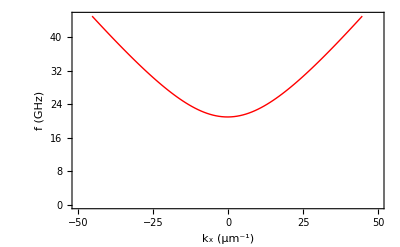

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-50 10^6,50 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->{0,45},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-50 10^6,50 10^6,1 10^6}]
```

{{-50,48.6828},{-49,47.8951},{-48,47.1101},{-47,46.328},{-46,45.5491},{-45,44.7734},{-44,44.0012},{-43,43.2327},{-42,42.4681},{-41,41.7077},{-40,40.9517},{-39,40.2004},{-38,39.454},{-37,38.713},{-36,37.9775},{-35,37.248},{-34,36.5249},{-33,35.8086},{-32,35.0994},{-31,34.3979},{-30,33.7046},{-29,33.02},{-28,32.3446},{-27,31.6792},{-26,31.0243},{-25,30.3807},{-24,29.7491},{-23,29.1303},{-22,28.5252},{-21,27.9346},{-20,27.3596},{-19,26.8012},{-18,26.2605},{-17,25.7385},{-16,25.2365},{-15,24.7558},{-14,24.2975},{-13,23.863},{-12,23.4538},{-11,23.071},{-10,22.7162},{-9,22.3906},{-8,22.0956},{-7,21.8324},{-6,21.6023},{-5,21.4063},{-4,21.2454},{-3,21.1204},{-2,21.032},{-1,20.9807},{0,20.9668},{1,20.9904},{2,21.0514},{3,21.1494},{4,21.2841},{5,21.4547},{6,21.6604},{7,21.9002},{8,22.173},{9,22.4777},{10,22.8129},{11,23.1774},{12,23.5698},{13,23.9887},{14,24.4327},{15,24.9006},{16,25.391},{17,25.9025},{18,26.4341},{19,26.9844},{20,27.5523},{21,28.1368},{22,28.7369},{23,29.3515},{24,29.9797},{25,30.6208},{26,31.2739},{27,31.9381},{28,32.613},{29,33.2977},{30,33.9916},{31,34.6943},{32,35.4051},{33,36.1235},{34,36.8491},{35,37.5814},{36,38.3201},{37,39.0647},{38,39.8149},{39,40.5703},{40,41.3307},{41,42.0958},{42,42.8652},{43,43.6388},{44,44.4162},{45,45.1973},{46,45.9819},{47,46.7697},{48,47.5606},{49,48.3543},{50,49.1508}}

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]]+If[freqs2[LL,ky a,0,0.5][[1]]<0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-50 10^6,50 10^6,1 10^6}]
```

{{-50,-0.467981},{-49,-0.459248},{-48,-0.450477},{-47,-0.441669},{-46,-0.432826},{-45,-0.423948},{-44,-0.415035},{-43,-0.406088},{-42,-0.397108},{-41,-0.388096},{-40,-0.379052},{-39,-0.369978},{-38,-0.360873},{-37,-0.351739},{-36,-0.342576},{-35,-0.333385},{-34,-0.324167},{-33,-0.314922},{-32,-0.305652},{-31,-0.296356},{-30,-0.287037},{-29,-0.277694},{-28,-0.268328},{-27,-0.25894},{-26,-0.249531},{-25,-0.240102},{-24,-0.230653},{-23,-0.221185},{-22,-0.211699},{-21,-0.202195},{-20,-0.192675},{-19,-0.183139},{-18,-0.173589},{-17,-0.164023},{-16,-0.154445},{-15,-0.144854},{-14,-0.13525},{-13,-0.125636},{-12,-0.116012},{-11,-0.106377},{-10,-0.0967346},{-9,-0.0870838},{-8,-0.0774259},{-7,-0.0677616},{-6,-0.0580917},{-5,-0.048417},{-4,-0.0387384},{-3,-0.0290566},{-2,-0.0193724},{-1,-0.00968659},{0,2.13163×10^-14},{1,0.00968659},{2,0.0193724},{3,0.0290566},{4,0.0387384},{5,0.048417},{6,0.0580917},{7,0.0677616},{8,0.0774259},{9,0.0870838},{10,0.0967346},{11,0.106377},{12,0.116012},{13,0.125636},{14,0.13525},{15,0.144854},{16,0.154445},{17,0.164023},{18,0.173589},{19,0.183139},{20,0.192675},{21,0.202195},{22,0.211699},{23,0.221185},{24,0.230653},{25,0.240102},{26,0.249531},{27,0.25894},{28,0.268328},{29,0.277694},{30,0.287037},{31,0.296356},{32,0.305652},{33,0.314922},{34,0.324167},{35,0.333385},{36,0.342576},{37,0.351739},{38,0.360873},{39,0.369978},{40,0.379052},{41,0.388096},{42,0.397108},{43,0.406088},{44,0.415035},{45,0.423948},{46,0.432826},{47,0.441669},{48,0.450477},{49,0.459248},{50,0.467981}}

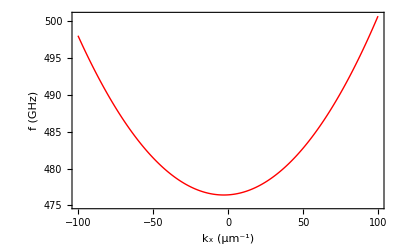

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[3]]>0,freqs2[LL,ky a,0,0.5][[3]],freqs2[LL,ky a,0,0.5][[4]]] },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->All,LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

### COMPARE TOP AND BOTTOM - the data

```mathematica
bot0={{-50,48.68280768259611},{-49,47.89505935223889},{-48,47.110073254749636},{-47,46.32801356341582},{-46,45.54905472559089},{-45,44.773382242794106},{-44,44.00119351497889},{-43,43.23269875350232},{-42,42.468121970168646},{-41,41.70770204423754},{-40,40.95169387702442},{-39,40.20036963747078},{-38,39.45402010538587},{-37,38.71295611727694},{-36,37.97751012138618},{-35,37.24803784487947},{-34,36.52492007840711},{-33,35.80856457911833},{-32,35.09940809389675},{-31,34.3979184998261},{-30,33.70459705608631},{-29,33.01998075985965},{-28,32.34464478749941},{-27,31.679205002095024},{-26,31.024320494978117},{-25,30.38069611957227},{-24,29.74908496589204},{-23,29.130290704460403},{-22,28.525169715798246},{-21,27.934632897077716},{-20,27.359647021598846},{-19,26.801235495642228},{-18,26.260478338716098},{-17,25.738511187923876},{-16,25.236523101969876},{-15,24.755752932392916},{-14,24.297484014798478},{-13,23.863036943821726},{-12,23.45376022302808},{-11,23.07101861906754},{-10,22.716179135870096},{-9,22.3905946187083},{-8,22.09558513805671},{-7,21.832417460140743},{-6,21.60228308797822},{-5,21.406275536308186},{-4,21.24536767026954},{-3,21.120390061434833},{-2,21.03201138699933},{-1,20.980721886033063},{0,20.96682079255229},{1,20.99040847650826},{2,21.05138377176671},{3,21.149446648217854},{4,21.284106070875538},{5,21.454692566896497},{6,21.6603747694159},{7,21.900179018448657},{8,22.173011004944293},{9,22.4776784321969},{10,22.81291374100669},{11,23.17739606872729},{12,23.56977177880603},{13,23.98867307701439},{14,24.432734407474335},{15,24.900606478553183},{16,25.390967908798032},{17,25.90253457712563},{18,26.434066847949364},{19,26.984374880035855},{20,27.552322255362597},{21,28.136828175201458},{22,28.73686845584164},{23,29.351475548432933},{24,29.979737782223246},{25,30.620798005173455},{26,31.27385177739213},{27,31.938145241740045},{28,32.612972780000646},{29,33.29767453847492},{30,33.991633894219284},{31,34.694274913633464},{32,35.405059844985196},{33,36.12348667733382},{34,36.84908678471542},{35,37.581422674337276},{36,38.32008584620513},{37,39.06469476997933},{38,39.814892982051354},{39,40.57034730107642},{40,41.33074616087664},{41,42.09579805549371},{42,42.86523009345471},{43,43.63878665462081},{44,44.41622814470834},{45,45.1973298407841},{46,45.98188082434512},{47,46.769682992371756},{48,47.56055014444799},{49,48.35430713858672},{50,49.150789111223425}};
```

```mathematica
bot1={{-100,498.0009766916759},{-99,497.5544965205821},{-98,497.112819489913},{-97,496.6759404521113},{-96,496.2438542775265},{-95,495.8165558555861},{-94,495.3940400959019},{-93,494.97630192926914},{-92,494.5633363088086},{-91,494.15513821101297},{-90,493.7517026368197},{-89,493.3530246126776},{-88,492.95909919155235},{-87,492.5699214540206},{-86,492.1854865092888},{-85,491.80578949622776},{-84,491.43082558432826},{-83,491.0605899748431},{-82,490.6950779016694},{-81,490.3342846323892},{-80,489.9782054692617},{-79,489.62683575017354},{-78,489.2801708496696},{-77,488.9382061798458},{-76,488.6009371913},{-75,488.26835937415126},{-74,487.9404682588472},{-73,487.61725941719965},{-72,487.298728463233},{-71,486.9848710540794},{-70,486.67568289094316},{-69,486.37115971984804},{-68,486.07129733265697},{-67,485.7760915677996},{-66,485.4855383112435},{-65,485.1996334972003},{-64,484.91837310904504},{-63,484.64175318011314},{-62,484.3697697944818},{-61,484.1024190877757},{-60,483.8396972479469},{-59,483.58160051604455},{-58,483.3281251869495},{-57,483.07926761016904},{-56,482.8350241905136},{-55,482.59539138885293},{-54,482.36036572283086},{-53,482.12994376753534},{-52,481.90412215620813},{-51,481.6828975808871},{-50,481.4662667930799},{-49,481.2542266044729},{-48,481.04677388742294},{-47,480.8439055757334},{-46,480.6456186651785},{-45,480.4519102141106},{-44,480.2627773440711},{-43,480.0782172403047},{-42,479.8982271524084},{-41,479.72280439480136},{-40,479.55194634728997},{-39,479.3856504555527},{-38,479.2239142317126},{-37,479.0667352547661},{-36,478.91411117109527},{-35,478.7660396949466},{-34,478.6225186088231},{-33,478.48354576402124},{-32,478.3491190809488},{-31,478.2192365496553},{-30,478.09389623013175},{-29,477.97309625274954},{-28,477.8568348186092},{-27,477.74511019992644},{-26,477.63792074038963},{-25,477.53526485541846},{-24,477.43714103257525},{-23,477.34354783179333},{-22,477.2544838857505},{-21,477.1699479000634},{-20,477.0899386536154},{-19,477.0144549987771},{-18,476.9434958616465},{-17,476.87706024229215},{-16,476.81514721492135},{-15,476.7577559281462},{-14,476.70488560509284},{-13,476.6565355436091},{-12,476.6127051164372},{-11,476.57339377130427},{-10,476.53860103109827},{-9,476.5083264939411},{-8,476.482569833304},{-7,476.46133079814297},{-6,476.4446092129069},{-5,476.4324049775895},{-4,476.4247180678492},{-3,476.42154853495884},{-2,476.42289650586895},{-1,476.4287621832},{0,476.439145845261},{1,476.4540478459314},{2,476.4734686147661},{3,476.49740865679905},{4,476.5258685525754},{5,476.5588489580364},{6,476.59635060444435},{7,476.6383742982223},{8,476.68492092092043},{9,476.7359914290006},{10,476.7915868536971},{11,476.85170830091846},{12,476.9163569510211},{13,476.98553405860173},{14,477.059240952338},{15,477.1374790347168},{16,477.22024978185715},{17,477.30755474324553},{18,477.3993955414372},{19,477.49577387185604},{20,477.5966915024373},{21,477.7021502733707},{22,477.81215209676253},{23,477.9266989563055},{24,478.0457929069689},{25,478.1694360745776},{26,478.29763065552453},{27,478.430378916309},{28,478.56768319321225},{29,478.7095458917999},{30,478.8559694865648},{31,479.00695652048375},{32,479.1625096045321},{33,479.3226314172504},{34,479.487324704207},{35,479.65659227760847},{36,479.8304370156758},{37,480.00886186223363},{38,480.1918698260824},{39,480.37946398050894},{40,480.5716474627184},{41,480.76842347322764},{42,480.9697952753447},{43,481.1757661944985},{44,481.38633961766476},{45,481.6015189927084},{46,481.82130782781553},{47,482.04570969075564},{48,482.2747282082695},{49,482.50836706536853},{50,482.74663000463454},{51,482.9895208255943},{52,483.23704338386017},{53,483.4892015905376},{54,483.74599941142725},{55,484.0074408662542},{56,484.27353002793484},{57,484.54427102177254},{58,484.8196680246961},{59,485.09972526445},{60,485.3844470187486},{61,485.6738376145013},{62,485.9679014269303},{63,486.2666428787434},{64,486.5700664392691},{65,486.87817662358503},{66,487.1909779916259},{67,487.50847514730333},{68,487.8306727376273},{69,488.15757545168304},{70,488.48918801984763},{71,488.8255152127241},{72,489.16656184031746},{73,489.512332750941},{74,489.8628328303652},{75,490.2180670007743},{76,490.57804021978086},{77,490.94275747949104},{78,491.31222380538105},{79,491.68644425540566},{80,492.0654239188969},{81,492.44916791551816},{82,492.83768139429776},{83,493.23096953251303},{84,493.6290375346582},{85,494.0318906313654},{86,494.43953407828775},{87,494.85197315513784},{88,495.2692131644692},{89,495.6912594306332},{90,496.1181172986766},{91,496.549792133246},{92,496.9862893174165},{93,497.4276142516118},{94,497.8737723524654},{95,498.3247690516806},{96,498.7806097949066},{97,499.24130004053205},{98,499.70684525862146},{99,500.17725092972995},{100,500.65252254368625}};
```

```mathematica
top0={{-50,48.2429180415644},{-49,47.46480567225879},{-48,46.68940592964096},{-47,45.91688392642795},{-46,45.14741505367276},{-45,44.38118576095048},{-44,43.61839440055013},{-43,42.859252140106804},{-42,42.10398395138361},{-41,41.35282967743314},{-40,40.60604518695057},{-39,39.863903619033074},{-38,39.12669672703362},{-37,38.39473632379326},{-36,37.668355836137685},{-35,36.94791197235732},{-34,36.233786505833045},{-33,35.526388178335395},{-32,34.82615472250623},{-31,34.13355500150426},{-30,33.4490912617388},{-29,32.773301486551134},{-28,32.1067618388176},{-27,31.450089165938444},{-26,30.80394354187767},{-25,30.169030800232807},{-24,29.54610500744259},{-23,28.935970806312653},{-22,28.339485544331936},{-21,27.757561079881384},{-20,27.191165140219407},{-19,26.641322077508526},{-18,26.109112848350534},{-17,25.595674017312326},{-16,25.10219556011239},{-15,24.629917233791023},{-14,24.18012326896889},{-13,23.7541351437925},{-12,23.353302234151442},{-11,22.97899017002697},{-10,22.632566810604335},{-9,22.315385850685832},{-8,22.02876820726438},{-7,21.77398149510117},{-6,21.552218070149365},{-5,21.364572311234422},{-4,21.212017962526147},{-3,21.09538649514649},{-2,21.015347510994566},{-1,20.97239220330113},{0,20.96682079255229},{1,20.99873467006041},{2,21.068033725722827},{3,21.17441902016814},{4,21.31740064108849},{5,21.496310267220835},{6,21.710317707696955},{7,21.95845049812178},{8,22.239615538870915},{9,22.5526217525212},{10,22.896202802074736},{11,23.269039047438657},{12,23.66977806975084},{13,24.097053284709258},{14,24.549500336062493},{15,25.02577112039796},{16,25.52454543069871},{17,26.04454030602525},{18,26.58451725747338},{19,27.143287575816085},{20,27.719715961233945},{21,28.312722720030358},{22,28.92128476100464},{23,29.544435615815654},{24,30.18126468285679},{25,30.830915869166347},{26,31.492585784118983},{27,32.16552161100561},{28,32.849018763405766},{29,33.54241841187558},{30,34.24510495077445},{31,34.95650345612105},{32,35.6760771804981},{33,36.40332511034419},{34,37.13777961216666},{35,37.87900417969924},{36,38.626591294150224},{37,39.380160401611974},{38,40.13935600965224},{39,40.90384590357978},{40,41.673319478854104},{41,42.447486186475786},{42,43.22607408764526},{43,44.008828509794505},{44,44.79551080171795},{45,45.58589717909994},{46,46.3797776572444},{47,47.17695506217573},{48,47.977244117888894},{49,48.780470602045895},{50,49.58647056566573}};
```

```mathematica
top1={{-100,498.2515363406103},{-99,497.79949675861246},{-98,497.352346002649},{-97,496.91007838516276},{-96,496.4726882264613},{-95,496.0401698559735},{-94,495.6125176134554},{-93,495.1897258500961},{-92,494.7717889297558},{-91,494.3587012301129},{-90,493.9504571438517},{-89,493.5470510797925},{-88,493.14847746404075},{-87,492.75473074115047},{-86,492.36580537529824},{-85,491.9816958513743},{-84,491.6023966760843},{-83,491.2279023791018},{-82,490.85820751422517},{-81,490.493306660365},{-80,490.13319442274803},{-79,489.7778654339335},{-78,489.42731435495904},{-77,489.08153587633507},{-76,488.74052471913814},{-75,488.404275636065},{-74,488.07278341249526},{-73,487.74604286745574},{-72,487.4240488547222},{-71,487.10679626377873},{-70,486.7942800208507},{-69,486.48649508984266},{-68,486.18343647338645},{-67,485.8850992137959},{-66,485.5914783939828},{-65,485.30256913847177},{-64,485.0183666142208},{-63,484.73886603176356},{-62,484.4640626458539},{-61,484.1939517566079},{-60,483.92852871022774},{-59,483.66778889999034},{-58,483.41172776701944},{-57,483.16034080126263},{-56,482.91362354219655},{-55,482.6715715797732},{-54,482.4341805552183},{-53,482.2014461617613},{-52,481.9733641454969},{-51,481.74993030616196},{-50,481.53114049789025},{-49,481.31699063003657},{-48,481.10747666772886},{-47,480.9025946328511},{-46,480.7023406045877},{-45,480.5067107201555},{-44,480.3157011756015},{-43,480.12930822625924},{-42,479.9475281876857},{-41,479.77035743612544},{-40,479.59779240921273},{-39,479.42982960653586},{-38,479.2664655903642},{-37,479.1076969861454},{-36,478.9535204831249},{-35,478.803932834924},{-34,478.6589308600886},{-33,478.5185114426115},{-32,478.382671532503},{-31,478.251408146249},{-30,478.1247183673968},{-29,478.0025993469439},{-28,477.8850483039037},{-27,477.77206252568635},{-26,477.6636393686199},{-25,477.5597762583042},{-24,477.4604706901018},{-23,477.3657202294817},{-22,477.2755225124846},{-21,477.18987524598316},{-20,477.1087762081774},{-19,477.0322232488592},{-18,476.9602142897522},{-17,476.89274732487075},{-16,476.82982042079755},{-15,476.77143171694905},{-14,476.71757942596497},{-13,476.668261833802},{-12,476.6234773001643},{-11,476.5832242585713},{-10,476.5475012167401},{-9,476.51630675666894},{-8,476.48963953487953},{-7,476.4674982826018},{-6,476.4498818059582},{-5,476.43678898606134},{-4,476.4282187792203},{-3,476.4241702169927},{-2,476.4246424063438},{-1,476.4296345297518},{0,476.439145845261},{1,476.453175686532},{2,476.47172346297157},{3,476.4947886596998},{4,476.5223708375936},{5,476.5544696333327},{6,476.5910847593853},{7,476.6322160039512},{8,476.6778632309994},{9,476.72802638016753},{10,476.78270546674855},{11,476.84190058161454},{12,476.90561189112236},{13,476.97383963697047},{14,477.046584136213},{15,477.1238457809745},{16,477.2056250384817},{17,477.2919224507298},{18,477.3827386344868},{19,477.47807428100856},{20,477.5779301558618},{21,477.6823070987615},{22,477.79120602329476},{23,477.9046279167002},{24,478.0225738396901},{25,478.14504492606085},{26,478.2720423825412},{27,478.40356748842015},{28,478.53962159531227},{29,478.6802061267698},{30,478.82532257803325},{31,478.9749725156121},{32,479.12915757701444},{33,479.2878794702832},{34,479.45113997371675},{35,479.61894093538814},{36,479.79128427280034},{37,479.9681719724139},{38,480.1496060892467},{39,480.3355887464246},{40,480.52612213472105},{41,480.72120851204613},{42,480.9208502030586},{43,481.12504959855767},{44,481.3338091550275},{45,481.54713139405015},{46,481.765018901957},{47,481.98747432900655},{48,482.214500389045},{49,482.44609985882414},{50,482.68227557738885},{51,482.9230304456476},{52,483.1683674255116},{53,483.41828953946356},{54,483.6727998698471},{55,483.9319015582397},{56,484.19559780479494},{57,484.4638918675016},{58,484.73678706157955},{59,485.0142867588029},{60,485.29639438667675},{61,485.58311342785777},{62,485.87444741930557},{63,486.17039995162577},{64,486.4709746682256},{65,486.77617526469635},{66,487.0860054878111},{67,487.4004691350073},{68,487.71957005336793},{69,488.04331213893295},{70,488.37169933581055},{71,488.704735635393},{72,489.0424250755305},{73,489.38477173961195},{74,489.73177975575965},{75,490.08345329592754},{76,490.43979657506117},{77,490.8008138501458},{78,491.1665094193575},{79,491.53688762113586},{80,491.9119528332652},{81,492.2917094719039},{82,492.67616199073166},{83,493.0653148799216},{84,493.45917266526527},{85,493.8577399070966},{86,494.2610211994294},{87,494.66902116894084},{88,495.0817444739369},{89,495.4991958033897},{90,495.92137987597033},{91,496.34830143900456},{92,496.7799652674368},{93,497.21637616281055},{94,497.65753895226527},{95,498.10345848747},{96,498.55413964360577},{97,499.0095873182545},{98,499.46980643041286},{99,499.9348019194067},{100,500.40457874376455}};
```

### Frequency asymmetry

```mathematica
asymTop0={{-50,-1.3435525241013266},{-49,-1.3156649297871041},{-48,-1.2878381882479317},{-47,-1.2600711357477792},{-46,-1.2323626035716373},{-45,-1.2047114181494578},{-44,-1.1771164011678223},{-43,-1.1495763696877006},{-42,-1.1220901362616473},{-41,-1.0946565090426432},{-40,-1.0672742919035372},{-39,-1.0399422845467043},{-38,-1.0126592826186211},{-37,-0.9854240778187133},{-36,-0.9582354580125383},{-35,-0.9310922073419192},{-34,-0.9039931063336155},{-33,-0.8769369320087961},{-32,-0.849922457991866},{-31,-0.8229484546167853},{-30,-0.7960136890356466},{-29,-0.7691169253244468},{-28,-0.7422569245881689},{-27,-0.7154324450671652},{-26,-0.6886422422413148},{-25,-0.6618850689335396},{-24,-0.6351596754141973},{-23,-0.6084648095030012},{-22,-0.5817992166727031},{-21,-0.5551616401489738},{-20,-0.5285508210145373},{-19,-0.501965498307559},{-18,-0.4754044091228451},{-17,-0.44886628871292444},{-16,-0.42234987058632},{-15,-0.3958538866069361},{-14,-0.36937706709360185},{-13,-0.3429181409167583},{-12,-0.3164758355993982},{-11,-0.29004887741168517},{-10,-0.2636359914704016},{-9,-0.23723590183536913},{-8,-0.21084733160653357},{-7,-0.18446900302060953},{-6,-0.15809963754758982},{-5,-0.1317379559864129},{-4,-0.10538267856234285},{-3,-0.07903252502165259},{-2,-0.052686214728261405},{-1,-0.026342466759281535},{0,2.1316282072803006*^-14},{1,0.026342466759281535},{2,0.052686214728261405},{3,0.07903252502165259},{4,0.10538267856234285},{5,0.1317379559864129},{6,0.15809963754758982},{7,0.18446900302060953},{8,0.21084733160653357},{9,0.23723590183536913},{10,0.2636359914704016},{11,0.29004887741168517},{12,0.3164758355993982},{13,0.3429181409167583},{14,0.36937706709360185},{15,0.3958538866069361},{16,0.42234987058632},{17,0.44886628871292444},{18,0.4754044091228451},{19,0.501965498307559},{20,0.5285508210145373},{21,0.5551616401489738},{22,0.5817992166727031},{23,0.6084648095030012},{24,0.6351596754141973},{25,0.6618850689335396},{26,0.6886422422413148},{27,0.7154324450671652},{28,0.7422569245881689},{29,0.7691169253244468},{30,0.7960136890356466},{31,0.8229484546167853},{32,0.849922457991866},{33,0.8769369320087961},{34,0.9039931063336155},{35,0.9310922073419192},{36,0.9582354580125383},{37,0.9854240778187133},{38,1.0126592826186211},{39,1.0399422845467043},{40,1.0672742919035372},{41,1.0946565090426432},{42,1.1220901362616473},{43,1.1495763696877006},{44,1.1771164011678223},{45,1.2047114181494578},{46,1.2323626035716373},{47,1.2600711357477792},{48,1.2878381882479317},{49,1.3156649297871041},{50,1.3435525241013266}};
asymBot0={{-50,-0.4679814286273114},{-49,-0.4592477863478308},{-48,-0.45047688969835065},{-47,-0.4416694289559331},{-46,-0.4328260987542265},{-45,-0.4239475979899936},{-44,-0.4150346297294547},{-43,-0.40608790111848947},{-42,-0.3971081232860669},{-41,-0.38809601125616666},{-40,-0.379052283852225},{-39,-0.36997766360563844},{-38,-0.36087287666548207},{-37,-0.35173865270239446},{-36,-0.3425757248189498},{-35,-0.3333848294578061},{-34,-0.32416670630830424},{-33,-0.3149220982154901},{-32,-0.30565175108844755},{-31,-0.29635641380736644},{-30,-0.28703683813297687},{-29,-0.2776937786152729},{-28,-0.2683279925012343},{-27,-0.2589402396450211},{-26,-0.249531282414015},{-25,-0.2401018856011845},{-24,-0.2306528163312045},{-23,-0.22118484397253013},{-22,-0.21169874004339562},{-21,-0.20219527812374238},{-20,-0.19267523376375095},{-19,-0.18313938439362687},{-18,-0.17358850923326585},{-17,-0.16402338920175197},{-16,-0.1544448068281561},{-15,-0.1448535461602667},{-14,-0.13525039267585726},{-13,-0.1256361331926641},{-12,-0.11601155577794842},{-11,-0.1063774496597496},{-10,-0.09673460513659293},{-9,-0.08708381348860073},{-8,-0.0774258668875838},{-7,-0.06776155830791453},{-6,-0.05809168143768062},{-5,-0.04841703058831115},{-4,-0.03873840060599676},{-3,-0.029056586783021032},{-2,-0.019372384767379458},{-1,-0.009686590475197931},{0,2.1316282072803006*^-14},{1,0.009686590475197931},{2,0.019372384767379458},{3,0.029056586783021032},{4,0.03873840060599676},{5,0.04841703058831115},{6,0.05809168143768062},{7,0.06776155830791453},{8,0.0774258668875838},{9,0.08708381348860073},{10,0.09673460513659293},{11,0.1063774496597496},{12,0.11601155577794842},{13,0.1256361331926641},{14,0.13525039267585726},{15,0.1448535461602667},{16,0.1544448068281561},{17,0.16402338920175197},{18,0.17358850923326585},{19,0.18313938439362687},{20,0.19267523376375095},{21,0.20219527812374238},{22,0.21169874004339562},{23,0.22118484397253013},{24,0.2306528163312045},{25,0.2401018856011845},{26,0.249531282414015},{27,0.2589402396450211},{28,0.2683279925012343},{29,0.2776937786152729},{30,0.28703683813297687},{31,0.29635641380736644},{32,0.30565175108844755},{33,0.3149220982154901},{34,0.32416670630830424},{35,0.3333848294578061},{36,0.3425757248189498},{37,0.35173865270239446},{38,0.36087287666548207},{39,0.36997766360563844},{40,0.379052283852225},{41,0.38809601125616666},{42,0.3971081232860669},{43,0.40608790111848947},{44,0.4150346297294547},{45,0.4239475979899936},{46,0.4328260987542265},{47,0.4416694289559331},{48,0.45047688969835065},{49,0.4592477863478308},{50,0.4679814286273114}};
```

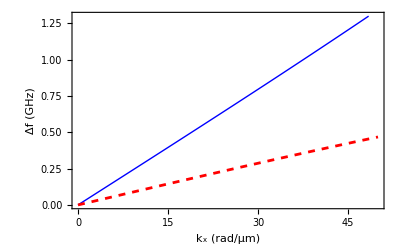

```mathematica
ListPlot[{asymTop0,asymBot0},PlotRange->{{0,50},{0,1.3}},Frame->True,FrameLabel->{"k_x (rad/μm)","Δf (GHz)"},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed]},FrameStyle->Directive[Black,Thick]]
```